```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
Clear[lc,m]
```

```mathematica
(*lc=2;*)
m=3;
γ=2`32;
σ2=-γ^2; (*σ2≤0*)
MatrixSize=50;
k[l_,lc_,m_]:=1/3 KroneckerDelta[l,lc]+2/3 √((2l+1)/(2lc+1))ClebschGordan[{l,m},{2,0},{lc,m}]ClebschGordan[{l,0},{2,0},{lc,0}];
```

```mathematica
K=Table[σ2 k[l,lc,m]+KroneckerDelta[l,lc]l(l+1),{lc,m,MatrixSize},{l,m,MatrixSize}]//N//Quiet;
```

```mathematica
A=Reverse[Eigenvalues[K]//N]
```

{11.5387,18.8864,28.5911,40.4232,54.3181,70.2479,88.1986,108.163,130.136,154.115,180.099,208.085,238.075,270.066,304.059,340.053,378.047,418.043,460.039,504.036,550.033,598.03,648.028,700.026,754.024,810.022,868.021,928.019,990.018,1054.02,1120.02,1188.02,1258.01,1330.01,1404.01,1480.01,1558.01,1638.01,1720.01,1804.01,1890.01,1978.01,2068.01,2160.01,2254.01,2350.01,2448.01,2548.01}

```mathematica
B=Table[
SpinWeightedSpheroidalEigenvalue[0,l,m,γ]//N,{l,m,MatrixSize}
]
```

{3.5387,10.8864,20.5911,32.4232,46.3181,62.2479,80.1986,100.163,122.136,146.115,172.099,200.085,230.075,262.066,296.059,332.053,370.047,410.043,452.039,496.036,542.033,590.03,640.028,692.026,746.024,802.022,860.021,920.019,982.018,1046.02,1112.02,1180.02,1250.01,1322.01,1396.01,1472.01,1550.01,1630.01,1712.01,1796.01,1882.01,1970.01,2060.01,2152.01,2246.01,2342.01,2440.01,2540.01}

```mathematica
A-B
-γ^2+2m γ
```

{8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.00492,8.00482}

8.

```mathematica
(*The eigenvalue is different between the BHPT and this papers definition*)
```

```mathematica
Genλms[lmax_,m_,γ_]:=Module[
{σ2 = -γ^2,M=m,Lmax=lmax,K,hold},
K=Table[σ2(1/3 KroneckerDelta[l,lc]+2/3 √((2l+1)/(2lc+1))Quiet[ClebschGordan[{l,m},{2,0},{lc,m}]ClebschGordan[{l,0},{2,0},{lc,0}]])+KroneckerDelta[l,lc]l(l+1),{lc,Abs[m],lmax},{l,Abs[m],lmax}];
Reverse[Eigenvalues[K]]
]
Genbms[lmax_,m_,γ_]:=Module[
{σ2 = -γ^2,M=m,Lmax=lmax,hold,K},
K=Table[σ2(1/3 KroneckerDelta[l,n]+2/3 √((2l+1)/(2n+1))Quiet[ClebschGordan[{l,m},{2,0},{n,m}]ClebschGordan[{l,0},{2,0},{n,0}]])+KroneckerDelta[l,n]l(l+1),{n,Abs[m],lmax},{l,Abs[m],lmax}];
hold = Reverse[Eigenvectors[K]];
hold
]

GenAllb[lmax_,lcmax_,γ_]:=Module[
{Lmax=lmax,Lcmax = lcmax, g= γ},
Table[Genbms[Lmax,m,g],{m,-Lcmax,Lcmax}]
]
```

```mathematica
lc=0;
m=0;
lmax = 100;
a = .9`32;
r0 = 4`32;
γ=a 1/(r0^(3/2)+a);
blclm=Genbms[lmax,m,γ];
(*blclm[[lc+1]]
Length[blclm[[lc+1]]]*)
(*Sum[blclm[[lc+1,l]]Y[l-1,m],{l,1,Length[blclm[[lc+1]]]}]*)
```

General::munfl: 3.81607 4.191270108861649773237613427382×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.85755 1.225723852398676231224593793772×10^-315 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.89859 3.4360150203750144824181321908×10^-322 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

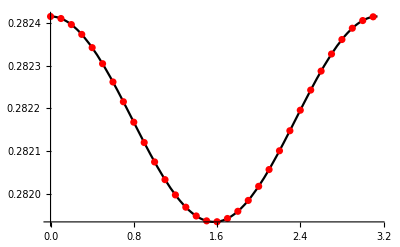

```mathematica
Show[
Plot[Sum[Abs[blclm[[lc+1,l]]]SphericalHarmonicY[l-1,m,θ,0],{l,1,Length[blclm[[lc+1]]]}],{θ,0,π},PlotStyle->Black],
ListPlot[Table[{θ,SpinWeightedSpheroidalHarmonicS[0,lc,m,γ,θ,0,Method->"SphericalExpansion"]//Quiet},{θ,0,π,.1}],PlotStyle->Red]
]
```

```mathematica
blcl10 = Genbms[lmax,10,γ];
blcl34 = Genbms[lmax,34,γ];
```

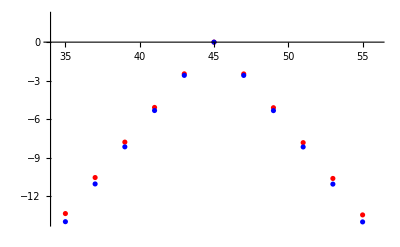

```mathematica
ListPlot[1/2{Log10[Abs[blcl10[[45]]]],Log10[Abs[blcl34[[45]]]]},Axes->True,PlotRange->{{34,56},{-14,2}},PlotStyle->{{Red,Thick},{Blue,Thick}}]
```

```mathematica
Bees=GenAllb[20,3,γ];
```

```mathematica
lc=0;
m=0;

Show[
Plot[Sum[Abs[Bees[[m+1+(Length[Bees]-1)/2,lc+1,l]]]SphericalHarmonicY[l-1,m,θ,0],{l,1,Length[Bees[[m +1+lc,lc+1]]]}],{θ,0,π},PlotStyle->Black],
ListPlot[Table[{θ,SpinWeightedSpheroidalHarmonicS[0,lc,m,γ,θ,0,Method->"SphericalExpansion"]//Quiet},{θ,0,π,.1}],PlotStyle->Red]
]
```

-Graphics-

```mathematica
Sdecomp[lc_,m_,γ_,θ_,b_]:=Sum[
Abs[b[[m+lc+1,lc+1,l]]]SphericalHarmonicY[l-1,m,θ,0],{l,1,Length[b[[m+lc+1,lc+1]]]}]
```

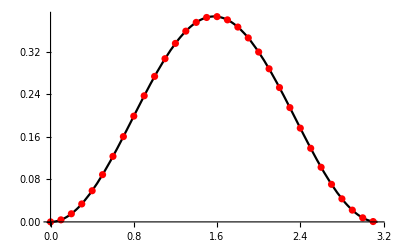

```mathematica
Show[
Plot[Sdecomp[lc,m,γ,θ,Bees],{θ,0,π},PlotStyle->Black],
ListPlot[Table[{θ,SpinWeightedSpheroidalHarmonicS[0,lc,m,γ,θ,0,Method->"SphericalExpansion"]//Quiet},{θ,0,π,.1}],PlotStyle->Red]
]
```